# C.W. Mills Acknowledgment Project Henry Hyunsuk Kim Mentor, Bob Nachbar WWS 2019

If Comte, Marx, Weber, and Durkheim are key figures in the discipline of sociology in general, C.W. Mills is a key person in U.S. contexts in particular. To study anything “sociological” requires the utilization of Mills’ concept of the “sociological imagination” (personal problems are in fact structural ills). Unsurprisingly, there is an annual book award in his honor, the “C. Wright Mills Award.” Though the field of bibliometrics is replete with citation analysis, a gap may exist regarding acknowledgements. Thus, my exploratory project concerns ascertaining what patterns may emerge with respect to acknowledgments in each and all of the books that have won the Mills Award. With the help of two RAs (Julian Petoske and Zury Rodriguez), the following book information was entered into an Excel spreadsheet: year of publication, title, author(s), persons acknowledged, author’s institution at the time of publication, where the author(s) completed her or his degrees (undergraduate and PhD), and the publisher. The data from the Excel file was then cleaned and manipulated via Mathematica at the 2019 Wolfram Summer Program with the invaluable help of two key persons (Bob Nachbar and Jesse Friedman). There was a total of 63 books, 68 authors (5 books were co-written), with a total of 2530 acknowledgments whereby 2369 were unique acknowledgements. 

Disclaimer: This notebook only runs when another notebook file, “1B. Mills Draft - UndataSet.nb” is evaluated first.

```mathematica
bookwinnersDataset=Import["C:\\Users\\hekim\\Box Sync\\wheaton\\Papers\\Works in Progress\\Testing 4.10 II.xlsx",{"Dataset",1},HeaderLines->1];
```

There was a total of 63 books, from 1964 to 2017. Authors (and co-authors) “thanked” 2530 persons in the preface of their books (2369 were unique acknowledgements). I have a different file that took up a lot of the staff’s time and because it is so long, and I could not decipher which aspects of that file I needed to copy into this one, after many failed attempts of copy/paste, I have to run that other notebook first, and then run this one.

```mathematica
yearsRange=MinMax[Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]]
```

{1964,2017}

```mathematica
totalBooks = integerYearBookWinnersSplitAuthors[[All, "Book Title"]]//Length
```

63

```mathematica
totalAuthors =integerYearBookWinnersSplitAuthors[[All, "Author"]]//Flatten//Length
```

68

```mathematica
totalAcnowledgments =integerYearBookWinnersSplitAuthors[[All, "Academic Acknowledgements"]]//Flatten//Length
```

2530

```mathematica
uniqueTotalAcnowledgments =integerYearBookWinnersSplitAuthors[[All, "Academic Acknowledgements"]]//Flatten//DeleteDuplicates//Length
```

2369

```mathematica
Keys@First@bookWinners//Column
```

Year
Book Title
Author
Academic Acknowledgements
Authors' Institution @ Publication
Author UG
Author PhD
Publisher

```mathematica
bookWinners=MapAt[Floor,bookWinners,{All,Key["Year"]}];
```

Below is a graph of the entire list of winners and persons they acknowledged. The graph depicts the core because the disconnected sub-graphs were removed in the hopes of providing better analyses.

```mathematica
gatheredBookWinners=GatherBy[bookWinnersClean,#["Book Title"]&];
```

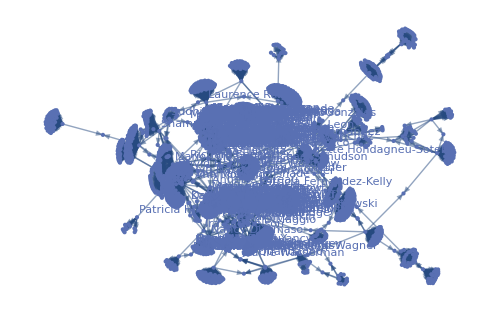

```mathematica
graphsPerYear=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersForYear[#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]];
accumulatingGraphs=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersBetweenYears[yearsRange[[1]],#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Range@@yearsRange];
accumulatingGraphs[2017]
```

Thread -> a list of pairs, FROM a pair of lists 
UpTo accounts  for “taking” “more” than the length of the list

```mathematica
ClearAll[gleanWellConnectedPersons]
Options[gleanWellConnectedPersons]={"count"->15,"measure"->BetweennessCentrality};
gleanWellConnectedPersons[graph_,OptionsPattern[]]:=
Module[{measure,count,namesAndCentralities,sortedList,topPersons},
measure=OptionValue["measure"];
count=OptionValue["count"];
namesAndCentralities=Thread[{VertexList[graph],measure[graph]}];
sortedList=ReverseSortBy[namesAndCentralities,Last];
topPersons=Take[sortedList,UpTo[count]];
DeleteCases[topPersons,{_,0.}]
]
```

### Tentative questions and answers from the respective charts

Where was the author when the book was published?
12 were in the UC system (respectively, Berkeley (10), San Diego (3), Santa Barbara (1), and Santa Cruz (1).

```mathematica
authorsSplitAtPublication = integerYearBookWinnersSplitAuthors[[All,"Authors' Institution @ Publication"]];
authorsSplitAtPublication;
Tally[%];
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

-Graphics-

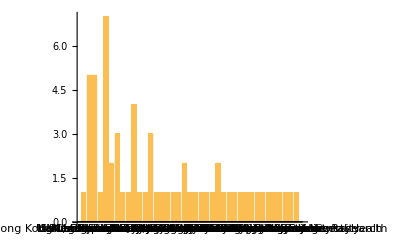

```mathematica
authorsSplitAtPublication;
Tally[%];
BarChart[Apply[Labeled,Reverse[%,2],{1}]]
```

```mathematica
integerYearBookWinnersSplitAuthors[[All, "Authors' Institution @ Publication"]]//Flatten//Sort//Counts
```

<|American Universty→1,Boston University→1,Brandeis University→1,Brooklyn College→1,Columbia University→5,Foothills College→1,George Mason University→1,Graduate Center, CUNY→2,Harvard University→5,Hong Kong University of Science and Technology→1,Massachusetts Institute of Technology→2,Michigan State University→1,Mills College→1,National Bureau of Economic Research→1,National Institute of Mental Health→1,New School for Social Research→1,Northeastern University→1,Northern Illinois University→1,Princeton University→4,Rutgers University→1,San Francisco State University→1,Southern Illinois University→1,Stockholm University→1,SUNY, Stony Brook→1,The American Socialist→1,UC, Berkeley→7,UC, San Diego→3,UC, Santa Barbara→1,UC, Santa Cruz→1,UNC, Chapel Hill→1,University of Arizona→1,University of Chicago→3,University of Cincinnati→1,University of Louisville→1,University of Oregon→1,University of Southern Maine→1,University of Toronto (CAN)→2,University of Virginia→1,USC→1|>

Where the did authors go to college?
No patterns seem to emerge with respect to where the authors went to college (4 went to Harvard and a total of 9 went to an Ivy League school). Although this does not necessarily disprove social reproduction, it does suggest that where one went to college may not necessarily be a good “predictor” in whether one wins the Mills Award. Unfortunately, this project was not able to ascertain the authors’ majors when the graduated from college.

```mathematica
authorsAtunderG=integerYearBookWinnersSplitAuthors[[All,"Author UG"]];
authorsSplitAtunderG = integerYearBookWinnersSplitAuthors[[All,"Author UG"]];
authorsSplitAtunderG;
Tally[%];
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

-Graphics-

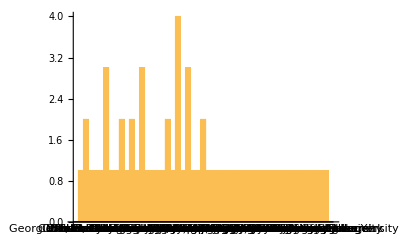

```mathematica
authorsSplitAtunderG;
Tally[%];
BarChart[Apply[Labeled,Reverse[%,2],{1}]]
```

```mathematica
integerYearBookWinnersSplitAuthors[[All, "Author UG"]]//Flatten//Sort//Counts
```

<|Albany State Teachers College→1,Barnard College→1,Brandeis University→2,Brooklyn College→1,Bryn Mawr College→1,Carleton College→2,Chinese University of Hong Kong→1,City College of New York→1,Colby College→1,Colorado College→2,Columbia University→3,Cornell University→1,George Washington Unniversity→1,Georgia Institute of Technology→1,Harvard University→4,Haverford College→1,Karl Marx University of Economics→1,Maryknoll College→1,Michigan State University→1,New School of Social Research→1,Northwestern University→1,Oberlin College→2,Occidental College→1,Ohio State University→1,Princeton University→1,Radcliffe College→1,Reed College→1,Rutgers University→1,Smith College→1,Stockholm University→1,Swarthmore College→1,Temple University→1,UC, San Diego→3,UC, Santa Cruz→3,UNC, Chapel Hill→1,University of Barcelona→1,University of Cape Town→1,University of Chicago→2,University of Denver→1,University of Guelph (CAN)→1,University of Illinois, Urbana-Champaign→1,University of Michigan→1,University of Ottawa (CA)→1,University of Sussex (UK)→1,University of Tennessee, Knoxville →1,UT, El Paso→1,UW, Madison→1,Western Michigan University→1,Wilberforce University→1|>

Where did the author get her/his PhD? 
Whereas an undergraduate degree may not have had much bearing on winning the Mills Award, where one received her or his PhD seems to have mattered. 11 winners went to Harvard. (Is there a way to extract the Ivy League Schools and tabulate them?) Unfortunately, this project did not include the major theme(s) of the sociology doctorate nor did it include the lead dissertation advisor and respective committee members.

```mathematica
authorsAtPhd=integerYearBookWinnersSplitAuthors[[All,"Author PhD"]];
authorsAtPhd;
Tally[%];
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

-Graphics-

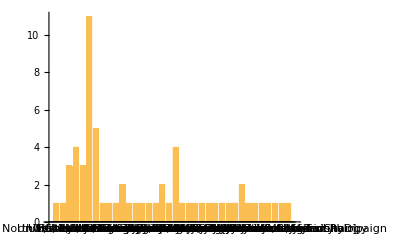

```mathematica
authorsAtPhd;
Tally[%];
BarChart[Apply[Labeled,Reverse[%,2],{1}]]
```

```mathematica
integerYearBookWinnersSplitAuthors[[All, "Author PhD"]]//Flatten//Sort//Counts
```

<|Brandeis University→1,Catholic University→1,Columbia University→4,Compultense University of Madrid→1,Graduate Center, CUNY→1,Harvard Medical School→1,Harvard University→11,Hungarian Academy of Sciences→1,Massachusetts Institute of Technology→1,MIT→1,New York University→1,Northwestern University→3,Northwestern University →1,Princeton University→2,Stanford University→1,Stockholm University→1,SUNY, Stony Brook→1,UC, Berkeley→5,UC, Davis→1,UC, Irvine→1,UC, San Diego→1,UC, San Francisco→1,UC, Santa Barbara→1,University of Alberta→1,University of Chicago→4,University of Illinois, Urbana-Champaign→1,University of London, SOAS→1,University of Michigan→1,University of Paris→1,University of Pensylvania→1,UT, Austin→1,UW, Madison→3,Washington State University→1,Washington University in St. Louis→2,Yale University→2,Missing[KeyAbsent,Author PhD]→1|>

Who was the Publisher? 
One publisher clearly stood out among the others, the University of California Press, which accounted for 13 winners. Unfortunately, this study did not include any information on the main editor(s) of the book winners.

```mathematica
authorsAndPub=integerYearBookWinnersSplitAuthors[[All,"Publisher"]];
authorsAndPub;
Tally[%];
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

-Graphics-

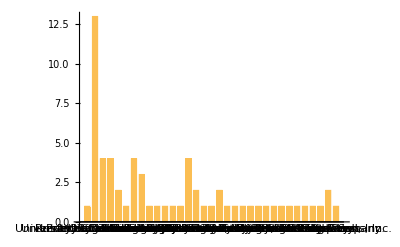

```mathematica
authorsAndPub;
Tally[%];
BarChart[Apply[Labeled,Reverse[%,2],{1}]]
```

```mathematica
integerYearBookWinnersSplitAuthors[[All, "Publisher"]]//Flatten//Sort//Counts
```

<|Aldine Publishing Company→1,Allen Lane→1,Basic Books→2,Basic Books, Inc.→1,Basic Books, Inc. Publishers→1,Cambridge University Press→4,Cornell University Press→1,D.C. Health and Company→1,Duke University Press→1,Farrar Straus & Giroux→1,Harvard University Press→3,Indiana University Press→1,John Wiley & Sons, Inc.→2,Little Brown→1,Monthly Review Press→1,Oxford University Press→4,Prentice-Hall→1,Prentice-Hall, Inc.→1,Princeton University Press→2,Routledge→2,Routledge and Kegan Paul Ltd.→1,Russell Sage Foundation→4,Rutgers University Press→1,The Belknap Press of Harvard University Press→1,The Free Press→1,The MIT Press→1,The University Press of Kentucky→1,University of California Press→13,University of Chicago Press→4,University of Minnesota→1,Vintage Books→1,Westview Press→1,Wisconsin University Press→1|>

SNA Metrics

Although almost twenty different SNA metrics were ascertained, most were unusable for various reasons. Thus, the five metrics that were explored in this study were: VertexOutDegree (VOD), VertexInDegree (VID), DegreeCentrality (DC), BetweennessCentrality (BC), and MeanNeighborDegree (MND). Because this project explores how authors “thanked” someone in the preface, I decided to employ a directed graph. That is, the author is the “sender” and the person acknowledged (or thanked) is the “recipient.” 

Accordingly, VOD tabulates each time an author “thanked” someone in preface and the VID measures each time a person was “thanked.” DC is the total number of ties with a given link, and thus may account for both VOD and VID (being a winning author does not preclude being “thanked.”) BC notes which node is on the shortest path between two other nodes. Thus, the greater the BC score, the greater the likelihood that it fills a “structural hole.” This is important regarding the flow of information in networks. Finally, MND provides the average number of nodes that is connected to a particular node in question.

Top score per given year

Below are the ListLinePlots for the highest respective SNA metric per specified year. VOD, DC, and MND show relatively stable growth until the end of the 20th century, where they spike in 1999.  BC shows a regular “step” growth with spikes at 2004 (215), 2013 (370), and 2014 (512). Perhaps VID shows the most “regular” pattern of growth, except for short dip in 1982 and 1983. (BC has gaps in 1964, 1965, 1982, and 1983.)

### VertexOutDegree

{20,20,20,20,20,20,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204}

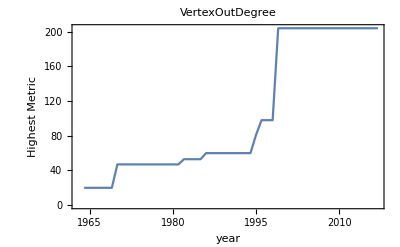

FittedModel[-14.2061+4.34622 x]

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsVertexOutDegree];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->VertexOutDegree]
LinearModelFit[lmfData,{1,x},x]
```

```mathematica
MapAt[Max,yearAndSNAs,{All,2}]//TableForm
```

1964 | 20
1965 | 20
1966 | 20
1967 | 20
1968 | 20
1969 | 20
1970 | 47
1971 | 47
1972 | 47
1973 | 47
1974 | 47
1975 | 47
1976 | 47
1977 | 47
1978 | 47
1979 | 47
1980 | 47
1981 | 47
1982 | 53
1983 | 53
1984 | 53
1985 | 53
1986 | 60
1987 | 60
1988 | 60
1989 | 60
1990 | 60
1991 | 60
1992 | 60
1993 | 60
1994 | 60
1995 | 81
1996 | 98
1997 | 98
1998 | 98
1999 | 204
2000 | 204
2001 | 204
2002 | 204
2003 | 204
2004 | 204
2005 | 204
2006 | 204
2007 | 204
2008 | 204
2009 | 204
2010 | 204
2011 | 204
2012 | 204
2013 | 204
2014 | 204
2015 | 204
2016 | 204
2017 | 204

### VertexInDegree

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7}

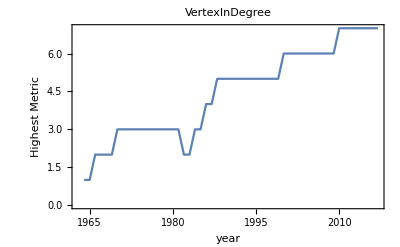

FittedModel[1.44235+0.109167 x]

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsVertexInDegree];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->VertexInDegree]
LinearModelFit[lmfData,{1,x},x]
```

```mathematica
MapAt[Max,yearAndSNAs,{All,2}]//TableForm
```

1964 | 1
1965 | 1
1966 | 2
1967 | 2
1968 | 2
1969 | 2
1970 | 3
1971 | 3
1972 | 3
1973 | 3
1974 | 3
1975 | 3
1976 | 3
1977 | 3
1978 | 3
1979 | 3
1980 | 3
1981 | 3
1982 | 2
1983 | 2
1984 | 3
1985 | 3
1986 | 4
1987 | 4
1988 | 5
1989 | 5
1990 | 5
1991 | 5
1992 | 5
1993 | 5
1994 | 5
1995 | 5
1996 | 5
1997 | 5
1998 | 5
1999 | 5
2000 | 6
2001 | 6
2002 | 6
2003 | 6
2004 | 6
2005 | 6
2006 | 6
2007 | 6
2008 | 6
2009 | 6
2010 | 7
2011 | 7
2012 | 7
2013 | 7
2014 | 7
2015 | 7
2016 | 7
2017 | 7

### DegreeCentrality

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

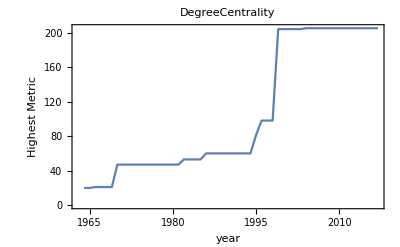

FittedModel[-14.2669+4.36055 x]

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsDegreeCentrality];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->DegreeCentrality]
LinearModelFit[lmfData,{1,x},x]
```

```mathematica
MapAt[Max,yearAndSNAs,{All,2}]//TableForm
```

1964 | 20
1965 | 20
1966 | 21
1967 | 21
1968 | 21
1969 | 21
1970 | 47
1971 | 47
1972 | 47
1973 | 47
1974 | 47
1975 | 47
1976 | 47
1977 | 47
1978 | 47
1979 | 47
1980 | 47
1981 | 47
1982 | 53
1983 | 53
1984 | 53
1985 | 53
1986 | 60
1987 | 60
1988 | 60
1989 | 60
1990 | 60
1991 | 60
1992 | 60
1993 | 60
1994 | 60
1995 | 81
1996 | 98
1997 | 98
1998 | 98
1999 | 204
2000 | 204
2001 | 204
2002 | 204
2003 | 204
2004 | 205
2005 | 205
2006 | 205
2007 | 205
2008 | 205
2009 | 205
2010 | 205
2011 | 205
2012 | 205
2013 | 205
2014 | 205
2015 | 205
2016 | 205
2017 | 205

### BetweennessCentrality

{-∞,-∞,18.,18.,18.,18.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,-∞,-∞,30.,30.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,215.,215.,215.,215.,215.,214.,214.,214.,214.,370.,512.,511.5,511.5,511.5}

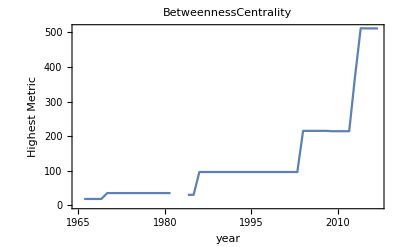

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{-∞,-∞,18.,18.,18.,18.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,-∞,-∞,30.,30.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,215.,215.,215.,215.,215.,214.,214.,214.,214.,370.,512.,511.5,511.5,511.5},{1,x},x]

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsBetweennessCentrality];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
LinearModelFit[lmfData,{1,x},x]
```

```mathematica
MapAt[Max,yearAndSNAs,{All,2}]//TableForm
```

1964 | -∞
1965 | -∞
1966 | 18.
1967 | 18.
1968 | 18.
1969 | 18.
1970 | 35.
1971 | 35.
1972 | 35.
1973 | 35.
1974 | 35.
1975 | 35.
1976 | 35.
1977 | 35.
1978 | 35.
1979 | 35.
1980 | 35.
1981 | 35.
1982 | -∞
1983 | -∞
1984 | 30.
1985 | 30.
1986 | 96.
1987 | 96.
1988 | 96.
1989 | 96.
1990 | 96.
1991 | 96.
1992 | 96.
1993 | 96.
1994 | 96.
1995 | 96.
1996 | 96.
1997 | 96.
1998 | 96.
1999 | 96.
2000 | 96.
2001 | 96.
2002 | 96.
2003 | 96.
2004 | 215.
2005 | 215.
2006 | 215.
2007 | 215.
2008 | 215.
2009 | 214.
2010 | 214.
2011 | 214.
2012 | 214.
2013 | 370.
2014 | 512.
2015 | 511.5
2016 | 511.5
2017 | 511.5

### MeanNeighborDegree

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

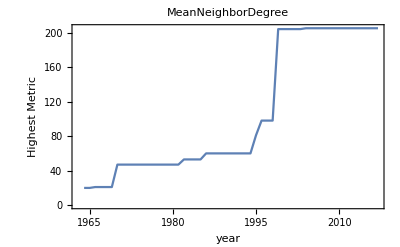

FittedModel[-14.2669+4.36055 x]

```mathematica
topConnectedPersonsMeanNeighborDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsMeanNeighborDegree];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->MeanNeighborDegree]
LinearModelFit[lmfData,{1,x},x]
```

```mathematica
MapAt[Max,yearAndSNAs,{All,2}]//TableForm
```

1964 | 20
1965 | 20
1966 | 21
1967 | 21
1968 | 21
1969 | 21
1970 | 47
1971 | 47
1972 | 47
1973 | 47
1974 | 47
1975 | 47
1976 | 47
1977 | 47
1978 | 47
1979 | 47
1980 | 47
1981 | 47
1982 | 53
1983 | 53
1984 | 53
1985 | 53
1986 | 60
1987 | 60
1988 | 60
1989 | 60
1990 | 60
1991 | 60
1992 | 60
1993 | 60
1994 | 60
1995 | 81
1996 | 98
1997 | 98
1998 | 98
1999 | 204
2000 | 204
2001 | 204
2002 | 204
2003 | 204
2004 | 205
2005 | 205
2006 | 205
2007 | 205
2008 | 205
2009 | 205
2010 | 205
2011 | 205
2012 | 205
2013 | 205
2014 | 205
2015 | 205
2016 | 205
2017 | 205

### Testing all respective SNA metrics via All years

Here I tried to extract all of the respective SNA metrics per node and year, and test what patterns emerged as a function of time. For example, from 1964-2017, there were 810 VertexInDegree scores. As proof of concept, I ran a simple LinearModelFit. Unfortunately, my Mathematica Language abilities precluded any attempts to run more sophisticated tests. All of the five SNA metrics in this study, based on a FittedModel data analysis, evinced a slightly positive slope (BC was the highest at +.352715). It is thus not surprising that there would be a positive correlation in a simple regression since the sample epitomizes a selection bias. However, why the BC was the greatest score needs further exploration. Is this because of Ronald Burt’s “structural holes” thesis or is there evidence of Adam Grant’s “give and take”?

### VertexOutDegree

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset;
vertexOutDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexOutDegree];
allVertexOutDegree=vertexOutDegree[[All,3]];
LinearModelFit[allVertexOutDegree,{1,x},x]
Length[vertexOutDegree]
```

FittedModel[-12.039+0.124308 x]

810

### VertexInDegree

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset;
vertexInDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexInDegree];
allVertexInDegree=vertexInDegree[[All,3]];
LinearModelFit[allVertexInDegree,{1,x},x]
Length[vertexInDegree]
```

FittedModel[0.790603+0.00413942 x]

810

### Degree Centrality

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset;
vertexDegreeCentrality =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
allVerteDegreeCentrality=vertexDegreeCentrality[[All,3]];
LinearModelFit[allVerteDegreeCentrality,{1,x},x]
Length[vertexDegreeCentrality]
```

FittedModel[-10.6632+0.122368 x]

810

### MeanNeighborDegree

```mathematica
topConnectedPersonsMeanNeighborDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs//Dataset;
vertexMeanNeighborDegree=Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsMeanNeighborDegree];
allVertexMeanNeighborDegree=vertexMeanNeighborDegree[[All,3]];
LinearModelFit[allVertexMeanNeighborDegree,{1,x},x]
Length[vertexMeanNeighborDegree]
```

FittedModel[-12.1918+0.290604 x]

810

### Betweenness Centrality

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset;
vertexBetweennessCentrality=Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsBetweennessCentrality];
allVertexBetweennessCentrality=vertexBetweennessCentrality[[All,3]];
LinearModelFit[allVertexBetweennessCentrality,{1,x},x]
Length[vertexBetweennessCentrality]
```

FittedModel[23.113+0.352715 x]

260

### MovingAverage (3-year Blocks) and MovingMedian, using only the top score per year

VOD have a high level of resemblance for both Moving metrics. There is a steady rate of growth with a big spike at “time” mid-30s. VID are also similar regarding a relatively steady rate of growth with a dip around “time” 20. DC show similar trends; there is a steady rate of growth with a big jump at “time” mid-30s. Both BC measures show a steady rate of growth with a big jump at “time” mid-40s. Finally, MND metrics both evince a steady rate of growth with a big jump at time mid-30s.

### VertexOutDegree

{20,20,20,20,20,20,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204}

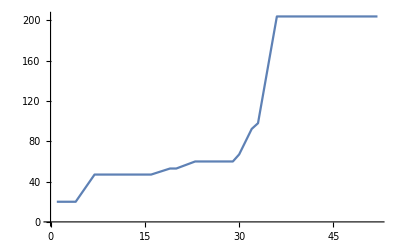

FittedModel[-14.2061+4.34622 x]

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset;
vertexOutDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexOutDegree];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{20,20,20,20,20,20,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204}

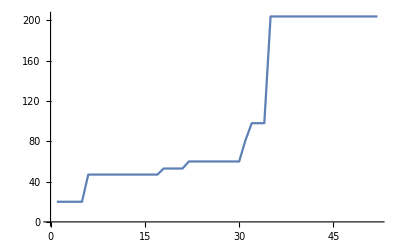

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset;
vertexOutDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexOutDegree];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

### VertexInDegree

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7}

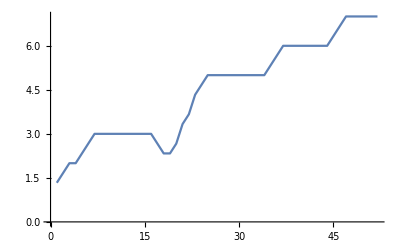

FittedModel[1.44235+0.109167 x]

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset;
vertexInDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexInDegree];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7}

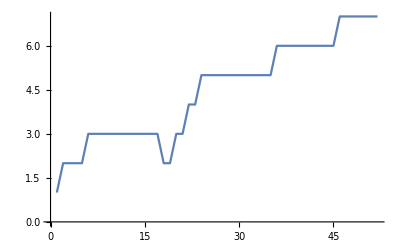

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset;
vertexInDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexInDegree];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

### DegreeCentrality

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

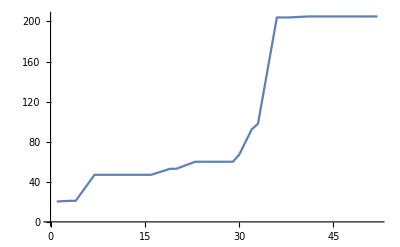

FittedModel[-14.2669+4.36055 x]

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset;
vertexDegreeCentrality =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

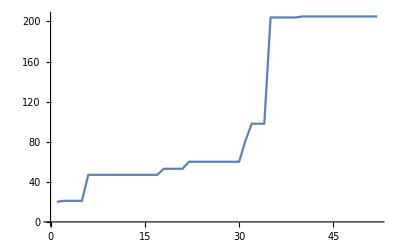

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset;
vertexDegreeCentrality =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

### BetweennessCentrality

{18.,18.,18.,18.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,30.,30.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,215.,215.,215.,215.,215.,214.,214.,214.,214.,370.,512.,511.5,511.5,511.5}

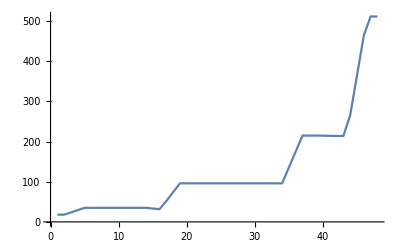

FittedModel[-62.3747+7.64411 x]

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset;
vertexBetweennessCentrality =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsBetweennessCentrality];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{18.,18.,18.,18.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,30.,30.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,215.,215.,215.,215.,215.,214.,214.,214.,214.,370.,512.,511.5,511.5,511.5}

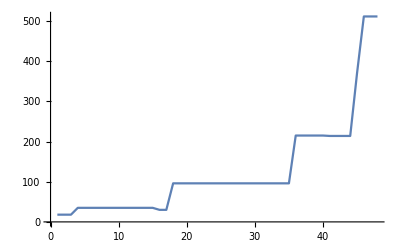

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset;
vertexBetweennessCentrality=tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsBetweennessCentrality];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

### MeanNeighborDegree

```mathematica
topConnectedPersonsMeanNeighborDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs//Dataset;
vertexMeanNeighborDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsMeanNeighborDegree];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

-Graphics-

FittedModel[-14.2669+4.36055 x]

```mathematica
topConnectedPersonsMeanNeighborDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs//Dataset;
vertexMeanNeighborDegree=tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsMeanNeighborDegree];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

-Graphics-

A TimesSeries function for ALL data points for specified SNA metrics, 1964-2017

### VertexOutDegree

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset;
vertexOutDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexOutDegree];
allVertexOutDegree=vertexOutDegree[[All,3]];
Length[%];
t=Range[%];
TimeSeries[allVertexOutDegree,{t}]
```

TimeSeries[…]

### VertextInDegree

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset;
vertexInDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexInDegree];
allVertexInDegree=vertexInDegree[[All,3]];
Length[%];
t=Range[%];
TimeSeries[allVertexInDegree,{t}]
```

TimeSeries[…]

### DegreeCentrality

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset;
vertexDegreeCentrality =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
allDegreeCentrality=vertexDegreeCentrality[[All,3]];
Length[%];
t=Range[%];
TimeSeries[allDegreeCentrality,{t}]
```

TimeSeries[…]

### BetweennessCentrality

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset;
vertexBetweennessCentrality =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
allBetweennessCentrality=vertexBetweennessCentrality[[All,3]];
Length[%];
t=Range[%];
TimeSeries[allBetweennessCentrality,{t}]
```

TimeSeries[…]

### MeanNeighborhoodDegree

```mathematica
topConnectedPersonsMeanNeighborhoodDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborhoodDegree]&/@accumulatingGraphs//Dataset;
vertexMeanNeighborhoodDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsMeanNeighborhoodDegree];
allMeanNeighborhoodDegree=vertexMeanNeighborhoodDegree[[All,3]];
Length[%];
t=Range[%];
TimeSeries[allMeanNeighborhoodDegree,{t}]
```

TimeSeries[…]

### Conclusions (needs some more work)

Did not try more tests, such as TimeSeriesModel or more elaborate tests such as Classify or PredictorFunction. However, this exploratory project does provide some proof of concept. For example, with the LinearModelFit results, these outputs can serve as a heuristic baseline to compare other respective studies (acknowledgements in a select group of prefaces). And, using one set of output (preferably a SNA metric) with another, one may explore the NonLinearModelFit function. I suppose if ratios of change, as a function of time could be mapped, then one may even explore (list some from your original proposal - which I had wanted to accomplish at the 2019 WSS but I ran out of time)